# Simulate consumer-resource models with externally-supplied resources

```mathematica
ClearAll["Global`*"]
```

```mathematica
ConsumerResourceModel[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    μo = parameters["μo"],
    σo = parameters["σo"],
    
    tEnd = simulation["tEnd"],
    (*noInitCond = simulation["noInitCond"],*)
    
    growth,
    consumption,
    death,
    influx,
    outflux,
    
    output

	},
	
	GenerateGrowthConsumption[] := Module[{
		xC,
		xG},
		
		xC = RandomVariate[NormalDistribution[0, 1], {M, S}]; 
		xG = RandomVariate[NormalDistribution[0, 1], {S, M}]; 
		
		growth = μg/M+σg/(√M)*xG;
		consumption = μc/M+σc/(√M)*(ρ*Transpose[xG] + √(1 - ρ^2)*xC);
		
		{growth, consumption}
	];
	
	SimulateDynamics[] := Module[{
		
		initR,
	    initN,
	    initRPerturbed,
	    initNPerturbed,
	    dRNdt,
	    solution,
	    solutionPerturbed,
	    evaluatedSolution,
	    evaluatedSolutionPerturbed,
	    distanceTrajectory (*,
	    trajectoryModel,
	    maxLE*)},
	    
	    initR = RandomVariate[UniformDistribution[{10^-8, 2/M}], M];
		initN = RandomVariate[UniformDistribution[{10^-8, 2/S}], S];
		
		dRNdt = {Resource'[t] == influx - outflux*Resource[t] - Resource[t]*(consumption.Species[t]) + 10^-8,
				 Species'[t] == Species[t]*(growth.Resource[t] - death) + 10^-8}; (*,
				 Resource[0] == initR,
				 Species[0] == initN};*)
			 
		solution = NDSolve[Join[dRNdt, {Resource[0] == initR, Species[0] == initN}],
						   {Resource, Species},
						   {t, tEnd},
						   Method -> "StiffnessSwitching", AccuracyGoal -> 10, PrecisionGoal -> 10][[1]];
	
		evaluatedSolution = {Table[Evaluate[Resource[t]/.solution], {t, Subdivide[0, tEnd, 200]}],
							 Table[Evaluate[Species[t]/.solution], {t, Subdivide[0, tEnd, 200]}]};
							 
		(*evaluatedSolution*)
							 
		initRPerturbed = initR + 10^-6;
		initNPerturbed = initN + 10^-6;
		
		solutionPerturbed = NDSolve[Join[dRNdt, {Resource[0] == initRPerturbed, Species[0] == initNPerturbed}],
								    {Resource, Species},
								    {t, tEnd},
								    Method -> "StiffnessSwitching", AccuracyGoal -> 10, PrecisionGoal -> 10][[1]];
	
		evaluatedSolutionPerturbed = {Table[Evaluate[Resource[t]/.solutionPerturbed], {t, Subdivide[0, tEnd, 200]}],
									  Table[Evaluate[Species[t]/.solutionPerturbed], {t, Subdivide[0, tEnd, 200]}]};
									  
		distanceTrajectory = MapThread[EuclideanDistance, {evaluatedSolution[[1]], evaluatedSolutionPerturbed[[1]]}],
									MapThread[EuclideanDistance, {evaluatedSolution[[2]], evaluatedSolutionPerturbed[[2]]}]
		  (*Log[10, Join[MapThread[EuclideanDistance, {evaluatedSolution[[1]], evaluatedSolutionPerturbed[[1]]}] + 
									      MapThread[EuclideanDistance, {evaluatedSolution[[2]], evaluatedSolutionPerturbed[[2]]}]]]*)
					
		(*LinearModelFit[{Subdivide[0, tEnd, 200], distanceTrajectory}, x, x]["BestFit"];*)
							 					 
		(*maxLE = {evaluatedSolution, maxLE}*)
	
	];
	
	{growth, consumption} = GenerateGrowthConsumption[];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	influx = μb + σb*RandomVariate[NormalDistribution[], M];
	outflux = μo + σo*RandomVariate[NormalDistribution[], M];
	
	output = SimulateDynamics[];
	
	output
];
```

```mathematica
simulationTest = ConsumerResourceModel[<|"M" -> 150, "S" -> 150,
										"ρ" -> 1.0, "μc" -> 1.0, "σc" -> 1.5, "μg" -> 1.0, "σg" -> 1.5,
										"μd" -> 1.0, "σd" -> 0.1,
										"μb" -> 1.0, "σb" -> 0.1,
										"μo" -> 1.0, "σo" -> 0.0|>, <|"tEnd" -> 50|>]
```

201

```mathematica
simulationTest[[1, 201]]
Last[simulationTest[[1]]]
```

{0.313433,0.346432,0.257572,0.344494,0.554026,0.375947,0.391528,0.236756,0.742008,0.423005,0.630552,0.303931,0.771759,0.419273,0.403775,0.636719,0.625923,0.253674,0.506191,0.283567,0.307552,1.11331,0.722703,0.171212,0.713726,0.22893,0.192392,0.415505,0.911963,0.349111,0.439714,0.353631,0.225379,0.68064,0.559025,0.593896,0.558808,0.258813,0.614612,0.702543,0.616318,0.219166,0.503624,0.733213,0.239693,0.199045,0.426891,0.553884,0.697598,0.822393,0.260495,0.556634,0.557254,0.264953,0.365108,0.397483,0.302587,0.248688,0.237491,0.732088,0.492353,0.222626,0.237013,0.310596,0.703556,0.484759,0.342763,0.414124,0.447395,0.329065,0.646689,0.486722,0.276722,0.884817,0.52174,0.928996,0.388598,1.06881,0.595675,0.684202,0.866929,0.628988,0.296303,0.488706,0.258698,0.242011,0.459558,0.464059,0.585107,0.183475,0.750852,0.537312,0.472954,0.151649,1.22776,0.339929,0.529378,0.664641,0.237227,0.33398,0.24618,0.365056,0.407196,0.537511,1.34839,0.377192,0.347356,0.430095,0.31005,0.441959,0.673683,0.60168,0.266735,0.418437,0.354235,0.185515,1.16697,0.776469,0.400318,0.333144,0.254764,0.472226,0.795325,0.27968,0.842949,0.849917,0.368447,0.481586,0.237776,0.372924,0.443582,0.319323,0.300824,0.456421,0.319889,0.378118,0.364709,1.27361,0.309769,0.161853,0.840782,0.253747,1.0198,1.22637,0.377756,0.629365,1.04111,0.318449,0.254082,0.209603}

{0.313433,0.346432,0.257572,0.344494,0.554026,0.375947,0.391528,0.236756,0.742008,0.423005,0.630552,0.303931,0.771759,0.419273,0.403775,0.636719,0.625923,0.253674,0.506191,0.283567,0.307552,1.11331,0.722703,0.171212,0.713726,0.22893,0.192392,0.415505,0.911963,0.349111,0.439714,0.353631,0.225379,0.68064,0.559025,0.593896,0.558808,0.258813,0.614612,0.702543,0.616318,0.219166,0.503624,0.733213,0.239693,0.199045,0.426891,0.553884,0.697598,0.822393,0.260495,0.556634,0.557254,0.264953,0.365108,0.397483,0.302587,0.248688,0.237491,0.732088,0.492353,0.222626,0.237013,0.310596,0.703556,0.484759,0.342763,0.414124,0.447395,0.329065,0.646689,0.486722,0.276722,0.884817,0.52174,0.928996,0.388598,1.06881,0.595675,0.684202,0.866929,0.628988,0.296303,0.488706,0.258698,0.242011,0.459558,0.464059,0.585107,0.183475,0.750852,0.537312,0.472954,0.151649,1.22776,0.339929,0.529378,0.664641,0.237227,0.33398,0.24618,0.365056,0.407196,0.537511,1.34839,0.377192,0.347356,0.430095,0.31005,0.441959,0.673683,0.60168,0.266735,0.418437,0.354235,0.185515,1.16697,0.776469,0.400318,0.333144,0.254764,0.472226,0.795325,0.27968,0.842949,0.849917,0.368447,0.481586,0.237776,0.372924,0.443582,0.319323,0.300824,0.456421,0.319889,0.378118,0.364709,1.27361,0.309769,0.161853,0.840782,0.253747,1.0198,1.22637,0.377756,0.629365,1.04111,0.318449,0.254082,0.209603}

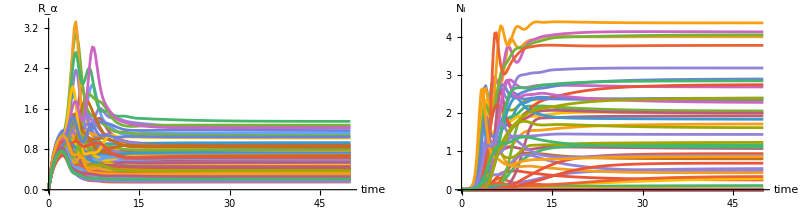

```mathematica
Rdynamics =Table[simulationTest[[1, All, alpha]], {alpha, 1, Length[simulationTest[[1, 1, All]]]}];
Ndynamics = Table[simulationTest[[2, All, alpha]], {alpha, 1, Length[simulationTest[[2, 1, All]]]}];
Show[GraphicsRow[{ListLinePlot[Rdynamics, AxesLabel -> {"time","R_α"}, DataRange -> {0, 50}, PlotRange -> All, AspectRatio -> 0.5],
				  ListLinePlot[Ndynamics, AxesLabel->{"time","N_i"}, DataRange -> {0, 50}, PlotRange -> All, AspectRatio -> 0.5]}],
				  ImageSize -> Full]
```